```mathematica
ClearAll["Global`*"]
```

```mathematica
NotebookSave[]
```

```mathematica
error=200;
```

#### define 4-simplices’ vertices

```mathematica
FourSimplices=Flatten[Table[Join[#,{i}]&/@(Join[{1,2},#]&/@Subsets[{3,4,5},{2}]),{i,6,7}],1];
```

```mathematica
Tets=Subsets[#,{4}]&/@FourSimplices;
```

```mathematica
TetFaces0=Table[Subsets[#,{3}]&/@Tets⟦i⟧,{i,Length[FourSimplices]}];
```

```mathematica
BDFaces=DeleteDuplicates[DeleteCases[Flatten[TetFaces0,2],{1,2,a_/;MemberQ[{3,4,5,6,7},a]}]];
```

```mathematica
InternalFaces=Complement[Flatten[TetFaces0,2],BDFaces];
```

```mathematica
lengthNumber=DeleteDuplicates[Flatten[Subsets[#,{2}]&/@FourSimplices,1]];
```

#### Define 4-simplices’ coordinate and related functions

```mathematica
bdypoints=SetPrecision[{{0.,0.,0.,0.},{-0.068,-0.21988127663727278,-0.5316227766016838,-1.331622776601684},{0.,0.,0.,-3.398088489694245},{-0.24028114141347542,-0.6936319083813028,-0.9809436521275706,-1.6990442448471226},{0.,0.,-2.942830956382712,-1.6990442448471226},{0.,-2.7745276335252114,-0.9809436521275706,-1.6990442448471226}}//N,error];
```

```mathematica
distance[V_,i_,j_]:=Block[{ge},ge=DiagonalMatrix[{-1,1,1,1}];(V⟦i⟧-V⟦j⟧).ge.(V⟦i⟧-V⟦j⟧)]
```

```mathematica
Heron2[a_,b_,c_]:=(a+b+c)/2((a+b+c)/2-a)((a+b+c)/2-b)((a+b+c)/2-c)
```

```mathematica
CM4D[{ls12_,ls13_,ls14_,ls15_,ls23_,ls24_,ls25_,ls34_,ls35_,ls45_}]:=({{0, ls12, ls13, ls14, ls15, 1}, {ls12, 0, ls23, ls24, ls25, 1}, {ls13, ls23, 0, ls34, ls35, 1}, {ls14, ls24, ls34, 0, ls45, 1}, {ls15, ls25, ls35, ls45, 0, 1}, {1, 1, 1, 1, 1, 0}})
V4sq[{ls12_,ls13_,ls14_,ls15_,ls23_,ls24_,ls25_,ls34_,ls35_,ls45_}]:=(-1)^4/(2^4(4!)^2)Det[CM4D[{ls12,ls13,ls14,ls15,ls23,ls24,ls25,ls34,ls35,ls45}]]
```

```mathematica
CM3D[{ls12_,ls13_,ls14_,ls23_,ls24_,ls34_}]:=({{0, ls12, ls13, ls14, 1}, {ls12, 0, ls23, ls24, 1}, {ls13, ls23, 0, ls34, 1}, {ls14, ls24, ls34, 0, 1}, {1, 1, 1, 1, 0}})
V3sq[{ls12_,ls13_,ls14_,ls23_,ls24_,ls34_}]:=(-1)^(3+1)/(2^3(3!)^2)Det[CM3D[{ls12,ls13,ls14,ls23,ls24,ls34}]]
```

```mathematica
CM2D[{ls12_,ls13_,ls23_}]:=({{0, ls12, ls13, 1}, {ls12, 0, ls23, 1}, {ls13, ls23, 0, 1}, {1, 1, 1, 0}})
V2sq[{ls12_,ls13_,ls23_}]:=(-1)^(2+1)/(2^2(2!)^2)Det[CM2D[{ls12,ls13,ls23}]]
```

```mathematica
Thetaij0[ls_,Simplex_]:=Block[{Tets,Tets2,length10,length1,length2,t,tbar,Vsigma,xbar,DVsigmaDtbar,Vtaua,Vtaub},
Tets=Subsets[Simplex,{4}];
Tets2=Subsets[Tets,{2}];
length1=Table[ls⟦Sequence@@#⟧&/@Subsets[Tets2⟦i,1⟧,{2}],{i,Length[Tets2]}];
length2=Table[ls⟦Sequence@@#⟧&/@Subsets[Tets2⟦i,2⟧,{2}],{i,Length[Tets2]}];
t=Intersection[#⟦1⟧,#⟦2⟧]&/@Tets2;
tbar=Complement[Simplex,#]&/@t;
length10=Table[If[i==j,xbar,ls⟦Sequence@@j⟧],{i,tbar},{j,Subsets[Simplex,{2}]}];
Vsigma=V4sq[#]&/@length10;
DVsigmaDtbar=Table[D[Vsigma⟦i⟧,xbar]/.xbar->ls⟦Sequence@@tbar⟦i⟧⟧,{i,Length[Vsigma]}];
Vtaua=V3sq[#]&/@length1;
Vtaub=V3sq[#]&/@length2;

Table[{DVsigmaDtbar⟦i⟧,Vtaua⟦i⟧,Vtaub⟦i⟧,t⟦i⟧},{i,Length[t]}]

]
```

```mathematica
Thetaij[ls0_,ls_,Simplex_]:=Block[{flat,curve},
flat=Thetaij0[ls0,Simplex];
curve=Thetaij0[ls,Simplex];
Table[{curve⟦i,4⟧,(Sign[flat⟦i,1⟧] √ExpandAll[curve⟦i,1⟧^2/flat[[i,1]]^2])/Expand[curve⟦i,1⟧/flat[[i,1]]]*ArcCosh[(4^2 √ExpandAll[curve⟦i,1⟧^2/flat[[i,1]]^2]*√(flat⟦i,1⟧^2))/(√ExpandAll[curve⟦i,2⟧/flat[[i,2]]]*√flat⟦i,2⟧*√ExpandAll[curve⟦i,3⟧/flat[[i,3]]]*√flat⟦i,3⟧)]},{i,Length[curve]}]//Simplify

]
```

```mathematica
deficitAngles[ls_,lvar_,n_]:=Block[{lvarmatrix,lsvar,angles,areas,anglesfinal},
lvarmatrix=ReplacePart[Array[0&,{7,7}],Join[{{1,2}->lvar},{{2,1}->lvar}]];lsvar=(Sqrt[ls]+lvarmatrix)^2;
angles=Flatten[Table[Thetaij[ls,lsvar,FourSimplices⟦i⟧],{i,6}],1];
areas=Sqrt[V2sq[lsvar⟦Sequence@@#⟧&/@Subsets[InternalFaces⟦n⟧,{2}]]];
anglesfinal=Sum[If[angles⟦j,1⟧==InternalFaces⟦n⟧,angles⟦j,2⟧,Unevaluated[Sequence[]]],{j,Length[angles]}];
{InternalFaces⟦n⟧,areas,angles,anglesfinal}
]
```

### Get vertices’ coordinate for the flat model and save the curved length square

```mathematica
Get[NotebookDirectory[]<>"vertex7Coor.wl"];
```

### Test result

#### test 4-simplex volume

```mathematica
lijvertex=Subsets[#,{2}]&/@FourSimplices;
```

```mathematica
ls0Square4=Table[distance[Vertex7,#⟦1⟧,#⟦2⟧]&/@i,{i,lijvertex}];
```

```mathematica
eigens4=Eigenvalues[CM4D[#]]&/@ls0Square4//N;
```

```mathematica
DeleteDuplicates[Join[{Count[#,u_/;u<0]},{Count[#,u_/;u>0]}]&/@eigens4]
```

{{4,2}}

```mathematica
DeleteDuplicates[#>0&/@(V4sq[#]&/@ls0Square4//N)]
```

{True}

#### test 3-simplex volume

```mathematica
lijtet=Subsets[#,{2}]&/@Flatten[Tets,1];
```

```mathematica
ls0Square3=Table[distance[Vertex7,#⟦1⟧,#⟦2⟧]&/@i,{i,lijtet}];
```

```mathematica
eigens3=Eigenvalues[CM3D[#]]&/@ls0Square3//N;
```

```mathematica
DeleteDuplicates[Join[{Count[#,u_/;u<0]},{Count[#,u_/;u>0]}]&/@eigens3]
```

{{4,1}}

```mathematica
DeleteDuplicates[#>0&/@(V3sq[#]&/@ls0Square3//N)]
```

{True}

#### test 2-simplex volume

```mathematica
lijTriangle=Subsets[#,{2}]&/@Flatten[TetFaces0,2];
```

```mathematica
ls0Square2=Table[distance[Vertex7,#⟦1⟧,#⟦2⟧]&/@i,{i,lijTriangle}];
```

```mathematica
eigens2=Eigenvalues[CM2D[#]]&/@ls0Square2//N;
```

```mathematica
DeleteDuplicates[Join[{Count[#,u_/;u<0]},{Count[#,u_/;u>0]}]&/@eigens2]
```

{{3,1}}

```mathematica
DeleteDuplicates[#>0&/@(V2sq[#]&/@ls0Square2//N)]
```

{True}

## Regge equation

```mathematica
reggeAction[ls0Square_,lvar_]:=Block[{lvarmatrix,ls,angles,variables,term1,term2,pp},
lvarmatrix=ReplacePart[Array[0&,{7,7}],Join[{{1,2}->lvar},{{2,1}->lvar}]];ls=(Sqrt[ls0Square]+lvarmatrix)^2;

term2=Sum[pp=Thetaij[ls0Square,ls,FourSimplices⟦i⟧];Sum[Sqrt[V2sq[ls⟦Sequence@@#⟧&/@Subsets[pp⟦j,1⟧,{2}]]]*pp[[j,2]],{j,Length[pp]}],{i,Length[FourSimplices]}];
term2
]
```

```mathematica
reggeEquation[ls0Square_,lvar_]:=Block[{tx12},
D[reggeAction[ls0Square,tx12],{tx12}]/.Thread[tx12->lvar]
]
```

### Flat case

```mathematica
ls0Square=Table[If[i==j,0,If[i==6&&j==7||i==7&&j==6,0,distance[Vertex7,i,j]]],{i,1,7},{j,1,7}];
```

```mathematica
FlatReggeAction=Block[{Xmin=-10^(-189/100),Xmax=10^(-26/10),ls35,r0,actionvsl,xx,yy},ls35=ls0Square;
r0=reggeAction[ls35,0];
actionvsl=reggeAction[ls35,t12];
yy=Table[actionvsl/.t12->X0,{X0,Xmin,Xmax,10^-5}];
xx=Table[X0,{X0,Xmin,Xmax,10^-5}];
Transpose[{xx,yy}]
];
```

```mathematica
flatcase=reggeEquation[ls0Square,t12];
```

```mathematica
Reggesoln1=t12/.FindRoot[flatcase==0,{t12,0},WorkingPrecision->50];
```

```mathematica
Reggesoln2=t12/.FindRoot[flatcase==0,{t12,-1/100},WorkingPrecision->50];
```

```mathematica
{Reggesoln1,Reggesoln2}//N
```

{7.04791×10^-52,-0.00809106}

```mathematica
Table[deficitAngles[ls0Square,Reggesoln1,i][[4]],{i,Length[InternalFaces]}]//N
```

{-1.86031×10^-50,1.05823×10^-49,-6.8111×10^-50,-4.75998×10^-50,-4.74479×10^-50}

```mathematica
Table[deficitAngles[ls0Square,Reggesoln2,i][[4]],{i,Length[InternalFaces]}]//N
```

{-0.2254,-1.40118,0.644468,0.418633,0.443107}

### Curved case

```mathematica
varyBD35Action[i_]:=Block[{Xmin=-10^(-189/100),Xmax=10^(-26/10),ls35,r0,actionvsl,xx,yy},ls35=ls0Square;
ls35[[3,5]]=(√ls0Square[[3,5]]+10^-i)^2;
ls35[[5,3]]=(√ls0Square[[5,3]]+10^-i)^2;
r0=reggeAction[ls35,0];
actionvsl=reggeAction[ls35,t12];
yy=Table[actionvsl/.t12->X0,{X0,Xmin,Xmax,10^-5}];
xx=Table[X0,{X0,Xmin,Xmax,10^-5}];
Transpose[{xx,yy}]
]
```

```mathematica
varyBD35Equation[i_]:=Block[{Xmin=-10^(-189/100),Xmax=10^(-26/10),ls35,tx12,fx,xx,zz},ls35=ls0Square;
ls35[[3,5]]=(√ls0Square[[3,5]]+10^-i)^2;
ls35[[5,3]]=(√ls0Square[[5,3]]+10^-i)^2;
fx=reggeEquation[ls35,t12];
zz=Table[fx/.t12->X0,{X0,Xmin,Xmax,10^-5}];
xx=Table[X0,{X0,Xmin,Xmax,10^-5}];
Transpose[{xx,zz}]
]
```

```mathematica
RAdatan3=varyBD35Action[3];
```

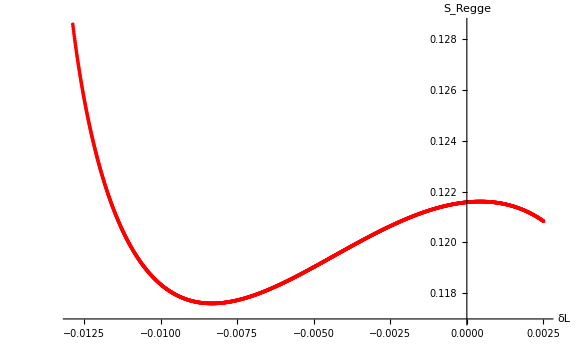

```mathematica
ListPlot[RAdatan3,PlotStyle->{Red,Thickness[0.03]},PlotRange->All,AxesLabel->{"δL","S_Regge"},AxesStyle->Thick,TicksStyle->Thick,ImageSize->Large,LabelStyle->Directive[Black,Bold,25],ImageSize->{600,600}]
```

```mathematica
dlvstheta=Table[ls35=ls0Square;
ls35[[3,5]]=(√ls0Square[[3,5]]+10^-3)^2;
ls35[[5,3]]=(√ls0Square[[5,3]]+10^-3)^2;{t12,Sqrt[Mean[(Table[deficitAngles[ls35,t12,j][[4]],{j,Length[InternalFaces]}])^2]]},{t12,-0.0025,0.0025,0.0001}];
```

```mathematica
min=Min[dlvstheta[[All,2]]]
```

0.0127854

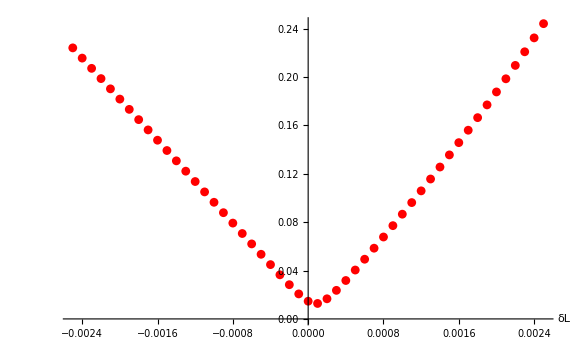

```mathematica
Show[ListPlot[dlvstheta,PlotRange->Full,PlotStyle->{Red,Thickness[0.01]},AxesLabel->{"δL"},AxesStyle->Thick,TicksStyle->Thick,ImageSize->Large,LabelStyle->Directive[Black,Bold,25],ImageSize->{600,600}]]
```

```mathematica
ls35=ls0Square;
ls35[[3,5]]=(√ls0Square[[3,5]]+10^-3)^2;
ls35[[5,3]]=(√ls0Square[[5,3]]+10^-3)^2;curvedcase=reggeEquation[ls35,t12];Reggecurve1=t12/.FindRoot[curvedcase==0,{t12,0},WorkingPrecision->50];
Reggecurve2=t12/.FindRoot[curvedcase==0,{t12,-1/100},WorkingPrecision->50];
```

```mathematica
{Reggecurve1,Reggecurve2}//N
```

{0.000439249,-0.00833517}

```mathematica
Save[NotebookDirectory[]<>"Reggesolution3.wl",{Reggecurve1,Reggecurve2}];
```

```mathematica
Save[NotebookDirectory[]<>"RAdatan3.wl",RAdatan3];
```

```mathematica
ls35=ls0Square;
ls35[[3,5]]=(√ls0Square[[3,5]]+10^-10)^2;
ls35[[5,3]]=(√ls0Square[[5,3]]+10^-10)^2;
Reggepseudo10=reggeAction[ls35,0];
```

```mathematica
Save[NotebookDirectory[]<>"Reggepseudo10.wl",Reggepseudo10];
```